# Sonifying Clave son – Exploring Musical Rhythm

Much of music from around the world is centered around characteristic rhythms called “timelines.” Here, we explore these timelines using Mathematica to sonify, visualize, and generate existing and original rhythms.

## Sonifcation

A timeline is simply a rhythm that repeats throughout a piece with no variation, giving a particular “feel” to the music that incorporates it in addition to serving as a timekeeper and structuring device for the musicians. Sometimes, these are called “rhythmic ostinatos.”

Here we generate the clave son (commonly just called clave) rhythm, a central facet of any salsa dance:

```mathematica
EmitSound[Sound[{SoundNote["Clap", 0.75],SoundNote["Clap", 0.75], SoundNote["Clap", 1.0], SoundNote["Clap", 0.5], SoundNote["Clap", 1.0]}]]
```

Sound familiar? That pattern is the foundation of nearly all Afro-Cuban music. Usually, it’s played on an instrument called claves which are two cylindrical pieces of resonant hardwood that produce a sound that cuts through the entire ensemble to communicate this pattern as a foundation to the music that’s going on around it.

The same rhythm, but this time with a claves sound instead of clapping. Here, we use a pure function to avoid retyping our instrument name each time:

```mathematica
EmitSound[Sound[{SoundNote[#, 0.75],SoundNote[#, 0.75], SoundNote[#, 1.0], SoundNote[#, 0.5], SoundNote[#, 1.0]}]] & ["Claves"]
```

Interestingly enough, this is same pattern is also known in rock and roll music as the “Bo Diddley beat,” named after rhythm and blues musician Bo Diddley.

Again, we have the same timeline, now with a bass drum:

```mathematica
EmitSound[Sound[{SoundNote[#, 0.75],SoundNote[#, 0.75], SoundNote[#, 1.0], SoundNote[#, 0.5], SoundNote[#, 1.0]}]] & ["BassDrum"]
```

Up until now, we’ve been generating these timelines by creating a sequence of SoundNotes with pre-determined lengths in seconds (take a look at the second argument of each SoundNote). However, in music we hear what many call a “pulse” or the thing you tap your foot to. The pulse is just a set of identical, repeated, and periodic stimuli.

Here’s a steady pulse (repeated 16 times) every 0.25 seconds:

```mathematica
EmitSound[Table[SoundNote[#, 0.25], 16]]& ["Clap"]
```

So if every rhythm is built off of this pulse, can we express our earlier clave rhythm in terms of this pulse? Of course! Let’s assume a pulse with a duration of 0.25. That means that each hit or onset will be a minimum of 0.25 seconds away from each other.

```mathematica
EmitSound[Sound[{SoundNote[#1, #2*3],SoundNote[#1, #2*3], SoundNote[#1, #2*4], SoundNote[#1, #2*2], SoundNote[#1, #2*4]}]] & ["Claves", 0.25]
```

So in that case, we’re expressing each onset as a certain multiple of our base pulse of 0.25. Because we’re dealing with percussion instruments, we could also just express every single pulse, with some being silent.

To “play” silence, we use an Instrument called None:

```mathematica
EmitSound[Sound[{
SoundNote[#1, #2],SoundNote[None, #2], SoundNote[None, #2], 
SoundNote[#1, #2],SoundNote[None, #2],SoundNote[None, #2],
SoundNote[#1, #2], SoundNote[None, #2],SoundNote[None, #2], SoundNote[None, #2],
SoundNote[#1, #2], SoundNote[None, #2],
SoundNote[#1, #2], SoundNote[None, #2], SoundNote[None, #2], SoundNote[None, #2]
}]] & ["Claves", 0.25]
```

The last thing we need to talk about is tempo. Tempo, in music, is just the speed of the pulse, usually measured in beats per minute. Well, in our previous example, we had 0.25 seconds per beat, so how do we find the number of beats per minute for that particular pulse length?

```mathematica
LinguisticAssistant/LinguisticAssistant /LinguisticAssistant
```

240. beats/min

We can also reverse this process. That is, given a tempo, we can calculate how long each pulse is in seconds.

```mathematica
(LinguisticAssistant/LinguisticAssistant)^-1
```

1/4 "

## Visualization

Up until now, we’ve just been listening to patterns without any way of visualizing the rhythms we’ve been playing with. But remember, our rhythms are just sequences of periodic pulses! So why not just represent each pulse by a square?

Here, we use the ArrayPlot function to plot an array of 16 0s:

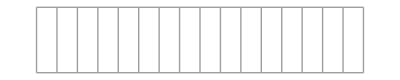

```mathematica
ArrayPlot[{Table[0, 16]}, Mesh->All]
```

With percussion instruments we only have onsets (hits) and rests, so we can just represent an onset as a filled in square while a rest is a blank square. If each square is 0.25 seconds in length, then to recreate our clave pattern, we need to fill in the 1st, 4th, 7th, 11th, 13th boxes.

We create the same diagram, but this time we add in onsets by using 1s (we also play the rhythm):

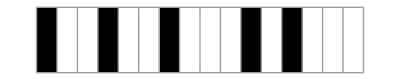

```mathematica
ArrayPlot[{{1, 0, 0, 1, 0, 0, 1, 0, 0,0, 1, 0, 1, 0, 0, 0}}, Mesh->All]
EmitSound[Sound[{SoundNote[#1, #2*3],SoundNote[#1, #2*3], SoundNote[#1, #2*4], SoundNote[#1, #2*2], SoundNote[#1, #2*4]}]] & ["Claves", 0.25]
```

Remember that these rhythmic timelines are cyclic: you reach the end and cycle back to the beginning. So another way to represent these would be to use a circular structure like a binary necklace.

Here we have the pulse represented by points on a circle and our pattern is represented by the nodes connected by the red edges (we use 0-indexed pulses because that’s how music theorists do it:

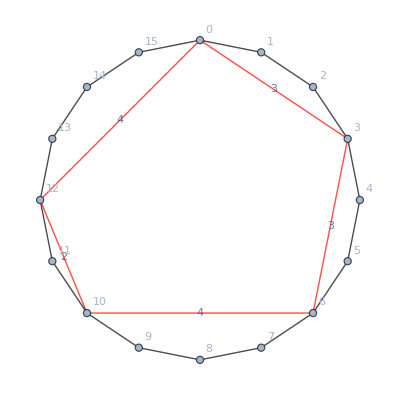

```mathematica
Graph[Reverse[Range[0, 15]], 
Join[Property[#,  EdgeStyle->{Black, Thin}]&/@ Table[i <-> Mod[i+1, 16] , {i, 0, 15}],Property[#,EdgeStyle->{Red, Thick}]&/@{0<->3, 3<->6, 6<->10, 10<->12, 12<->0}],
GraphLayout->"CircularEmbedding", VertexLabels->All,EdgeLabels->{0<->3->3, 3<->6->3, 6<->10->4, 10<->12->2, 12<->0->4}]
```

Checkout the shape formed by the pattern in our cyclic representation. Maybe humans find rhythms with irregular polygon shapes more interesting than those with regular polygon representations... We won’t explore that idea here, but maybe try it on your own!

We’ll focus on the first type of visualization, often called a TUBS (Time Unit Box System) diagram for the rest of our exploring.

## Generation

An interesting consequence of our TUBS diagram is any easy to extract binary representation of our rhythm. It’s simple: 0 is a rest and a 1 is an onset. In fact, if we take a look at our earlier TUBS generation code, that’s exactly how we gave ArrayPlot our rhythmic pattern!

```mathematica
ArrayPlot[{{1, 0, 0, 1, 0, 0, 1, 0, 0,0, 1, 0, 1, 0, 0, 0}}, Mesh->All]
```

-Graphics-

Of course, we also need a way to actually sonify this new way of representing our rhythms. Below, we write a function that takes in two arguments, a binary array and a tempo, and creates a Sound that we can hear.

```mathematica
sonifyRhythm[instrument_, pattern_, tempo_]:= Sound[SoundNote[#, (tempo/60)^-1]& /@ (pattern /. {0 -> None, 1 -> instrument})]
```

Having this binary form of our rhythm means we can easily do computations on it without leaving our pulse-based system.

Rotate (shift beats):

{1,0,0,1,0,0,1,0,0,0,1,0,1,0,0,0}

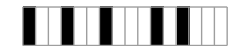

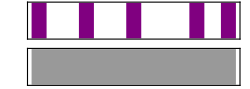

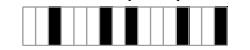

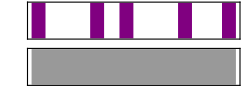

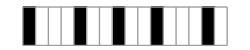

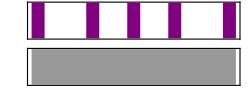

```mathematica
clave = {1, 0, 0, 1, 0, 0, 1, 0, 0,0, 1, 0, 1, 0, 0, 0}
ArrayPlot[{clave}, Mesh->All, PlotLabel->"clave"]
sonifyRhythm["Claves", clave, 240.0]

ArrayPlot[{RotateLeft[clave,4]}, Mesh->All, PlotLabel->"RotateLeft[clave, 4]"]
sonifyRhythm["Claves", RotateLeft[clave, 4], 240.0]

ArrayPlot[{RotateRight[clave,4]}, Mesh->All, PlotLabel->"RotateRight[clave, 4]"]
sonifyRhythm["Claves", RotateRight[clave, 4], 240.0]
```

Invert:

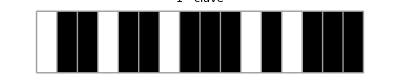

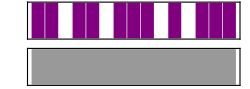

```mathematica
ArrayPlot[{1-clave}, Mesh->All, PlotLabel->"1 - clave"]
sonifyRhythm["Claves", 1-clave, 240.0]
```

In fact, these are common rules that musicians and composers use to change up rhythms in real music.

We could get even fancier by generating a new rhythm after each playthrough by using 1-D cellular automata rules.

Using rule 30 (the top row is the first generation, the 2nd row the second generation, and so forth):

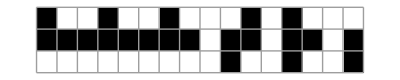

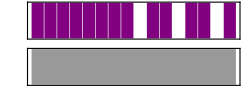
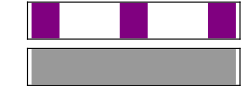
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[CellularAutomaton[30, clave, 2], Mesh->All]
sonifyRhythm["Claves", #, 240]& /@ CellularAutomaton[30, clave, 2]
```

## Bonus: Cross beats

In complex pieces of music, particularly Jazz, musicians often like to create “rhythmic complexity” by creating polyrhythms. We didn’t get a chance to explore the idea of macro-beats in our previous explorations, but suffice it to say for now that often times we hear groupings of pulses instead of a the lowest common micro-pulse. It’s this macro-beat that we usually end up tapping our foot to. The cool thing about these macro-pulses is that they can be made up of different numbers of micro-pulses based on the music you’re playing. This leads to a concept of rhythmic meter which we don’t have time to explore in-depth. Instead, let’s talk about “cross beats” which rely on the ear hearing a simultaneous expression of two different kinds of macro beats.

Pretend you’re a drummer from Ghana. You’re given 20 micro-pulses and asked to play on the first of the 20 pulses and three other evenly spaced pulses. In other words, you have four evenly spaced onsets.

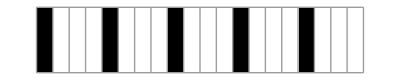

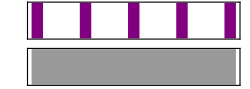

```mathematica
ArrayPlot[{Table[If[Mod[i, 4] == 1, 1, 0], {i,20}]}, Mesh->All]
sonifyRhythm["Claves",Table[If[Mod[i, 4] == 1, 1, 0], {i,20}], 240]
```

Now do the same thing, except you need to play on 4 other evenly spaced pulses. In other words, you have five evenly spaced onsets.

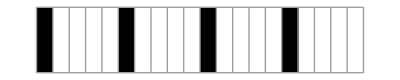

-Graphics-

```mathematica
ArrayPlot[{Table[If[Mod[i, 5] == 1, 1, 0], {i,20}]}, Mesh->All]
sonifyRhythm["Claves",Table[If[Mod[i, 4] == 1, 1, 0], {i,20}], 240]
```

If these two players were to play at the same time, the human ear (and brain) senses the tension between the two different rhythmic sub divisions. This is a really common technique in West African drum music.

Here we have one drummer play 4 evenly space hits while the other plays 5 evenly spaced hits (these are grouped together into one instrument for simplicity):

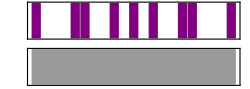

```mathematica
sonifyRhythm["Claves",(Table[If[Mod[i, 4] == 1, 1, 0],{i, 21}] + Table[If[Mod[i, 5] == 1, 1, 0],{i, 21}]) /. {2->1},240]
```

```mathematica
Manipulate[
ArrayPlot[{Table[If[Mod[i, a] == 1, 1, 0],{i, LCM[b,a]+1}], Table[If[Mod[i, b] == 1, 1, 0],{i, LCM[b,a]+1}]} , Mesh->All],
{a, 1, 10, 1}, {b,1,10, 1}
]
```

## Things we didn’t get to

We’ve barely scratched the surface of musical rhythm. This was just meant as an intro to seeing how we could formally express, visualize, and generate new rhythms using the Wolfram Language. A great next step would be to explore musical meter, a concept that lots of beginning musicians have trouble with.

Further Explorations

Musical Geometry
Musical Structure (Voice Leading and Part Writing)
Classical Fugue Analysis
Composing from the Greats: Using Machine Learning to Generate Musical Compositions

Authorship information

Connor Bain

June 23, 2017 - v1.0

connorbain@u.northwestern.edu